# Maximum Likelihood Analyses

Generally the procedure is as follows.

1. Begin defining the model as a probability distribution of counts, as a function of some variable (Q) and parameters.
2. Write a function assuming each value of the function is a separate term with its own Q value.  The likelihood is the geometric series of each of these.
3. Take the logarithm of the function so the log-likelihood can take advantage of the laws of logarithms to swap products for sums.
4. Differentiate with respect to each parameter of interest.  
5. Set the LHS to zero (the differental of the log-likelihood is zero at the maximum!).  Rearrange the equation in terms of the parameter.  You now have a bunch of equations - one for each parameter - as a function of the variable (e.g. Q).
6. Stream each value of Q into the equations and obtain increasingly accurate estimates for each value.

## Logarithm Laws

These might be handy at some point, might as well code them up.

```mathematica
logExpand[xpr_]:=Module[
{ans,lr1,lr2,lr3,lr4},
lr1=Log[x_^y_]:>y*Log[x];
lr2=Log[x_/y_]:>Log[x]-Log[y];
lr3=Log[x_*y_]:>Log[x]+Log[y];
lr4=Log[Product[x_,{j_,k_}]]:>Sum[Log[x],{j,k}];
Return[xpr//.{lr1,lr2,lr3,lr4}]
]
```

```mathematica
testfunc = Log[Product[1/(κ^2+Subscript[Q,i]^2),{i,k}]]
```

Log[∏_i^k 1/(κ^2+Q_i^2)]

```mathematica
logExpand[testfunc]
```

∑_i^k -Log[κ^2+Q_i^2]

```mathematica
N[ⅇ/2]
```

1.35914

## Gaussian - A Standard Example

```mathematica
normal = 1/(σ * Sqrt[2*Pi])*Exp[-(Subscript[x, i]-μ)^2/(2*σ^2)];
gauss=∏_i^n normal;
lgauss=Log[gauss];
lgauss =logExpand[lgauss];
dm =D[lgauss,μ];
ddm=D[dm, μ]
ds=D[lgauss,σ];
dds=D[ds,σ]
dmds=D[dm, σ]
dsdm =D[ds, μ]
```

-n/σ^2

∑_i^n (1/σ^2-(3 (-μ+x_i)^2)/σ^4)

∑_i^n (2 μ-2 x_i)/σ^3

∑_i^n (2 μ-2 x_i)/σ^3

General integral:

```mathematica
Assuming[{μ ∈Reals, σ ∈Reals,σ > 0,xmin ∈ Reals, xmin>0, xmax ∈Reals,xmax>0}, Integrate[1/(σ * Sqrt[2*Pi])*Exp[-(x-μ)^2/(2*σ^2)], {x, xmin, xmax}]]
```

1/2 (Erf[(xmax-μ)/(√2 σ)]-Erf[(xmin-μ)/(√2 σ)])

```mathematica
fisherIM = -{{dds, dsdm}, {dmds, ddm}};
MatrixForm[fisherIM]
```

(-∑_i^n (1/σ^2-(3 (-μ+x_i)^2)/σ^4) | -∑_i^n (2 μ-2 x_i)/σ^3
-∑_i^n (2 μ-2 x_i)/σ^3 | n/σ^2)

```mathematica
variances = 1/n * Inverse[fisherIM]
```

{{1/(σ^2 (-(∑_i^n (2 μ-2 x_i)/σ^3)^2-(n ∑_i^n (1/σ^2-(3 (-μ+x_i)^2)/σ^4))/σ^2)),(∑_i^n (2 μ-2 x_i)/σ^3)/(n (-(∑_i^n (2 μ-2 x_i)/σ^3)^2-(n ∑_i^n (1/σ^2-(3 (-μ+x_i)^2)/σ^4))/σ^2))},{(∑_i^n (2 μ-2 x_i)/σ^3)/(n (-(∑_i^n (2 μ-2 x_i)/σ^3)^2-(n ∑_i^n (1/σ^2-(3 (-μ+x_i)^2)/σ^4))/σ^2)),-(∑_i^n (1/σ^2-(3 (-μ+x_i)^2)/σ^4))/(n (-(∑_i^n (2 μ-2 x_i)/σ^3)^2-(n ∑_i^n (1/σ^2-(3 (-μ+x_i)^2)/σ^4))/σ^2))}}

## Generalised Sharp or Fractal Porod Scattering

What we actually need to do here is use a proper power law MLE estimation, which fortunately exists already.  It’s not by the same person as the R package by the same name, but it looks like it implements the same functionality.  In that case, the underlying maths is the Pareto Distribution so we can steal all of that

```mathematica
Clear["α"];
porod = (α-1)/xmin*(x/xmin)^-α;
int=Integrate[porod,x]
rg2=int/.x->xmax;
rg1 =int/.x->xmin;
rg=rg2-rg1
rgs=Assuming[{α∈Reals,xmin∈Reals,x∈Reals, xmax∈Reals,α>0, xmin>0, x>0, x>xmin, xmax>0, xmax>xmin}, Simplify[rg]]
mycdf=Assuming[{α∈Reals,xmin∈Reals,x∈Reals, xmax∈Reals,α>0, xmin>0, x>0, x>xmin, xmax>0, xmax>xmin},Integrate[porod, {x,xmin,xmax}]]/.xmax->x
myquantile=x/.Flatten[Solve[p==mycdf,x]][[1]]
```

(x (x/xmin)^-α (-1+α))/(xmin (1-α))

-(-1+α)/(1-α)+(xmax (xmax/xmin)^-α (-1+α))/(xmin (1-α))

1-(xmin/xmax)^(-1+α)

1-(xmin/x)^(-1+α)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(1-p)^(-1/(-1+α)) xmin

```mathematica
Solve[p==1-(x/xmin)^(-α+1),x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(1-p)^(1/(1-α)) xmin}}

```mathematica
nevents=3190;
flat=RandomReal[1,nevents];
events=Table[myquantile/.{α->4,xmin->0.001,p->flat[[i]]},{i,nevents}];
```

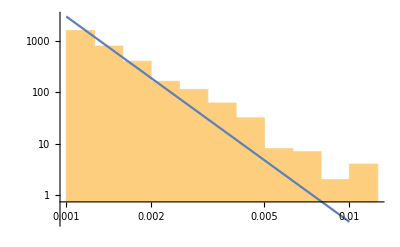

```mathematica
hst=Histogram[events,"Log","LogCount"];
line=LogLogPlot[porod/.{α->4, xmin->0.001}, {x, 0.001, 0.01}];
Show[hst,line]
```

This is exactly what I see in my python code, it seems that the slope of the line is not the same as the slope of the data even though the α is consistent in the equations.

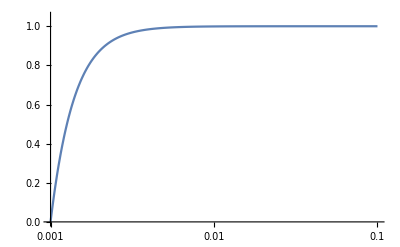

```mathematica
LogLinearPlot[1-(x/xmin)^(-α+1)/.{α->4, xmin->0.001},{x,0.001,0.1},PlotRange->{Automatic,{0,1.05}}]
```

```mathematica
LogLinearPlot[mycdf/.{α->4, xmin->0.001}, {x,0.001, 0.1},PlotRange->{Automatic,{0,1.05}}]
```

-Graphics-

```mathematica
myquantile/.{α->4,xmin->0.001}
```

0.001/(1-p)^(1/3)

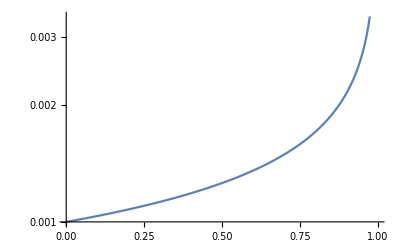

```mathematica
LogPlot[myquantile/.{α->4,xmin->0.001},{p,0,1}]
```

## Lorenzian

This is actually a Cauchy distribution.  Standard scattering function for a classical phase transition.  Wikipedia explains how to solve this with maximum likelihood (https://en.wikipedia.org/wiki/Cauchy_distribution ) but it requires a numerical solution in any case.

```mathematica
lor = 1/(π γ (1+Q^2/γ^2))
```

1/(π (1+Q^2/γ^2) γ)

```mathematica
FullSimplify[lor]
```

γ/(π Q^2+π γ^2)

So A is γ/π multiplied by some scaling factor for unnormalised data and we can ditch the π.  Most importantly,  κ = γ , so it’s all great.

```mathematica
Clear["κ"]
pq=Product[(κ/Pi)/(κ^2+Subscript[Q,i]^2),{i,n}]
lpq=logExpand[Log[pq]]
dlpq=D[lpq,κ]
ddlpq=D[dlpq,κ]
```

∏_i^n κ/(π (κ^2+Q_i^2))

∑_i^n (-Log[π]+Log[κ]-Log[κ^2+Q_i^2])

∑_i^n (1/κ-(2 κ)/(κ^2+Q_i^2))

∑_i^n (-1/κ^2+(4 κ^2)/((κ^2+Q_i^2)^2)-2/(κ^2+Q_i^2))

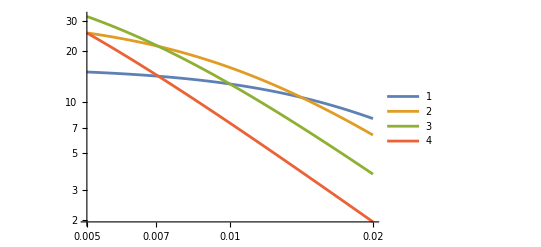

```mathematica
lorGraph=LogLogPlot[
{lor/.γ->1.0/50.0,
lor/.γ->1.0/100.0,
lor/.γ->1.0/200.0,
lor/.γ->1.0/400.0},{Q,0.005,0.02},PlotLegends->True]
```

```mathematica
lorInt50=Integrate[lor/.γ->1.0/50.0,{Q, 0.005, 0.02}]
lorInt100=Integrate[lor/.γ->1.0/100.0,{Q, 0.005, 0.02}]
lorInt200=Integrate[lor/.γ->1.0/200.0,{Q, 0.005, 0.02}]
lorInt400=Integrate[lor/.γ->1.0/400.0,{Q, 0.005, 0.02}]
```

0.172021

0.204833

0.172021

0.108

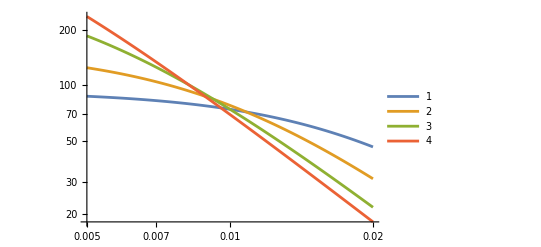

```mathematica
lorGraph=LogLogPlot[
{lor/ lorInt50/.γ->1.0/50.0 ,
lor/lorInt100/.γ->1.0/100.0,
lor/lorInt200/.γ->1.0/200.0,
lor/lorInt400/.γ->1.0/400.0},{Q,0.005,0.02},PlotLegends->True]
```

```mathematica
cdf = 1/π*ArcTan[(x-x0)/κ]+ 1/2
qtl = x0 + κ * Tan[π*(p-1/2)]
```

1/2+ArcTan[(x-x0)/κ]/π

x0+κ Tan[(-1/2+p) π]

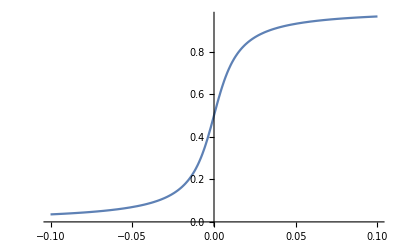

```mathematica
Plot[cdf/.{x0->0, κ->1.0/90.0},{x, -0.1, 0.1}]
```

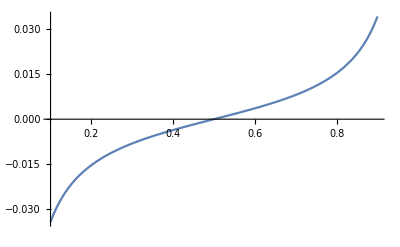

```mathematica
Plot[qtl/.{x0->0, κ->1/90},{p,0.1,0.9}]
```

General integral of the curve

```mathematica
lorInt =
```

For SANS we need half a CDF because Q starts at 0 and not -∞

(2 ArcTan[x/κ])/π

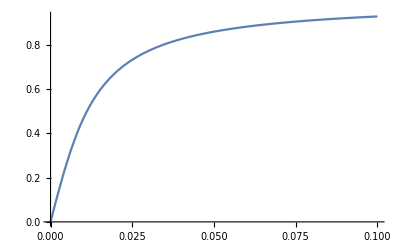

```mathematica
halfcdf = 2/π*ArcTan[x/κ]
Plot[halfcdf/.{x0->0, κ->1.0/90.0},{x,0, 0.1}, PlotRange->All]
```

General integral over range:

```mathematica
lorIntegral=Assuming[{γ ∈Reals,xmin ∈ Reals, xmin>0, xmax ∈Reals,xmax>0, γ>0}, Integrate[lor, {Q, xmin, xmax}]]
```

(ArcTan[xmax/γ]-ArcTan[xmin/γ])/π

Check with analytical integral

```mathematica
lor=κ/(π Q^2+π κ^2)
cdf=Assuming[{κ ∈Reals, κ>0}, Integrate[lor, {Q, -Infinity, x}]]
```

κ/(π Q^2+π κ^2)

1/2+ArcTan[x/κ]/π

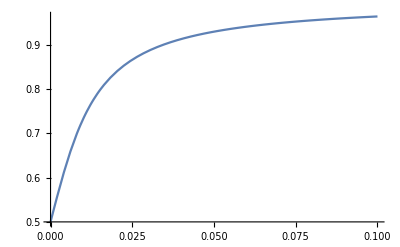

```mathematica
Plot[cdf/.κ->1.0/90.0, {x, 0, 0.1}, PlotRange->All]
```

My guess above for the halfCDF is actually wrong.  I need the analytical one here in fact.  Lets check the half quantile

```mathematica
qtl = κ*Tan[(p-1/2)*π]
```

κ Tan[(-1/2+p) π]

```mathematica
Plot[qtl/.{ κ->1/90},{p,0.1,0.9}]
```

-Graphics-

## Double Lorentzian

The main problem here is that we are out of wikipedia / mathworld territory.  I guess that the right answer is a sum of arctans but we must verify it analytically of course.

```mathematica
lord=κ/(π Q^2+π κ^2)+κ2/(π Q^2+π κ2^2)
cdf=Assuming[{κ ∈Reals,κ2∈Reals,  κ>0, κ2>0}, Integrate[lord, {Q, -Infinity, x}]]
```

κ/(π Q^2+π κ^2)+κ2/(π Q^2+π κ2^2)

(π+ArcTan[x/κ]+ArcTan[x/κ2])/π

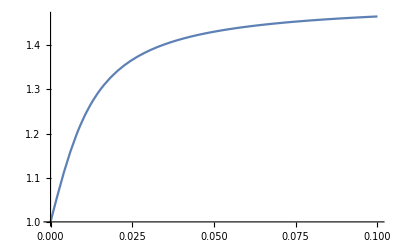

```mathematica
Plot[cdf/.{κ->1.0/90.0, κ2->110.0}, {x, 0, 0.1}, PlotRange->All]
```

This distribution is no longer normalised, we need a normalisation factor

```mathematica
siz=Assuming[{κ ∈Reals,κ2∈Reals,  κ>0, κ2>0}, Integrate[lord, {Q, -Infinity, Infinity}]]
```

2

OK that makes perfect sense because each lorentzian is normalised to unity, the sum of two of them must add to 2!!!

## Lorentzian Plus Background

```mathematica
lorb=κ/(π Q^2+π κ^2)+b
```

b+κ/(π Q^2+π κ^2)

```mathematica
pq=Product[b+(κ/Pi)/(κ^2+Subscript[Q,i]^2),{i,n}];
lpq=logExpand[Log[pq]]
dlpqk=D[lpq,κ]
ddlpqk=D[dlpq,κ]
dlpqb=D[lpq,b]
ddlpqb=D[dlpq,b]
```

∑_i^n Log[b+κ/(π (κ^2+Q_i^2))]

∑_i^n (-(2 κ^2)/(π (κ^2+Q_i^2)^2)+1/(π (κ^2+Q_i^2)))/(b+κ/(π (κ^2+Q_i^2)))

∑_i^n (((8 κ^3)/(π (κ^2+Q_i^2)^3)-(6 κ)/(π (κ^2+Q_i^2)^2))/(b+κ/(π (κ^2+Q_i^2)))+(-(2 κ^2)/(π (κ^2+Q_i^2)^2)+1/(π (κ^2+Q_i^2))) ((2 κ^2)/(π (κ^2+Q_i^2)^2 (b+κ/(π (κ^2+Q_i^2)))^2)-1/(π (κ^2+Q_i^2) (b+κ/(π (κ^2+Q_i^2)))^2)))

∑_i^n 1/(b+κ/(π (κ^2+Q_i^2)))

∑_i^n -(-(2 κ^2)/(π (κ^2+Q_i^2)^2)+1/(π (κ^2+Q_i^2)))/((b+κ/(π (κ^2+Q_i^2)))^2)

```mathematica
eq1=lorb/.{κ->0.02, b->0.1}
eq2=lorb/.{κ->0.1, b->0.2}
```

0.1+0.02/(0.00125664+π Q^2)

0.2+0.1/(0.0314159+π Q^2)

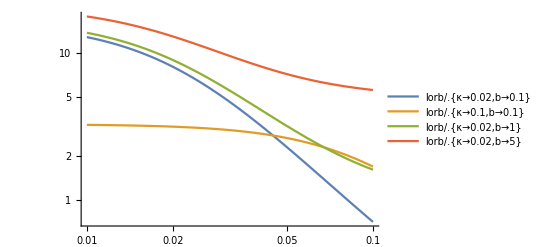

```mathematica
LogLogPlot[
{
lorb/.{κ->0.02, b->0.1},
lorb/.{κ->0.1, b->0.1},
lorb/.{κ->0.02, b->1},
lorb/.{κ->0.02, b->5}
} ,{Q,0.01, 0.1}, PlotLegends->LineLegend["Expressions"]]
```

## Aharony - Pytte

Random quenched fields, random anisotropy: Phys Rev B 27 (1983) p 5872.  Aharony and Pytte’s probability curve is not normalised, so that’s the first thing we need to do.

```mathematica
A = κ^2* s*B;
B = κ/π;
pc = κ/π*(B/(κ^2+Q^2)+A/((κ^2+Q^2)^2))
normFactor=Assuming[{κ ∈Reals, κ>0, s ∈ Reals, s> 0}, Integrate[pc, {Q, -Infinity, Infinity}]]
```

(κ ((s κ^3)/(π (Q^2+κ^2)^2)+κ/(π (Q^2+κ^2))))/π

((2+s) κ)/(2 π)

```mathematica
pc = pc / normFactor
```

(2 ((s κ^3)/(π (Q^2+κ^2)^2)+κ/(π (Q^2+κ^2))))/(2+s)

```mathematica
Expand[pc]
```

(2 s κ^3)/(π (2+s) (Q^2+κ^2)^2)+(2 κ)/(π (2+s) (Q^2+κ^2))

```mathematica
cdf=Assuming[{κ ∈Reals, κ>0}, Integrate[pc, {Q, -Infinity, x}]]
```

1/2+(s x κ)/(π (2+s) (x^2+κ^2))+ArcTan[x/κ]/π

```mathematica
Expand[cdf]
```

1/2+(s x κ)/(π (2+s) (x^2+κ^2))+ArcTan[x/κ]/π

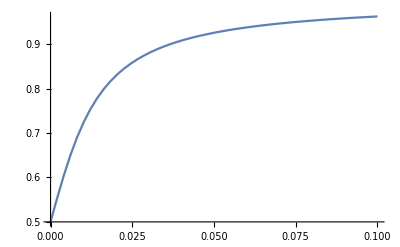

```mathematica
Plot[cdf/.{κ->1/80, s->0.1}, {x, 0, 0.1},PlotRange->All]
```

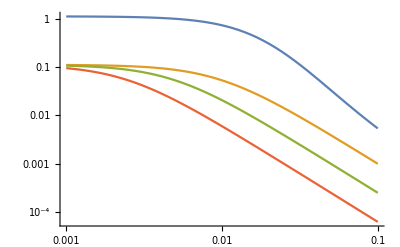

```mathematica
apGraph=LogLogPlot[
{pc/.{κ->1.0/50.0, s->10},\
pc/.{κ->1.0/100.0, s->0.1},
pc/.{κ->1.0/200.0, s->0.1},
pc/.{κ->1.0/400.0, s->0.1}},{Q,0.001,0.1}]
```

```mathematica
pc/.{Q->#}
```

(s κ^2)/((κ^2+#1^2)^2)+1/(κ^2+#1^2)

```mathematica
pFunc =(s κ^2)/((κ^2+#1^2)^2)+1/(κ^2+#1^2)
```

(s κ^2)/((κ^2+#1^2)^2)+1/(κ^2+#1^2)

```mathematica
quant = InverseFunction[pFunc]
```

InverseFunction[(s κ^2)/((κ^2+#1^2)^2)+1/(κ^2+#1^2)]

There is no inverse function for this (as I expected) so I need to resort to a numerical method.  Iterative methods seem to be the main solution, so maybe the base class quantile function will do an iterative computation and the quantile can be overloaded if it can be derived.

```mathematica
pq=Product[pc/.Q->Subscript[Q,i],{i,n}]
lpq=logExpand[Log[pq]]
```

∏_i^n (2 ((s κ^3)/(π (κ^2+Q_i^2)^2)+κ/(π (κ^2+Q_i^2))))/(2+s)

∑_i^n (Log[2]-Log[2+s]+Log[(s κ^3)/(π (κ^2+Q_i^2)^2)+κ/(π (κ^2+Q_i^2))])

## Sphere

```mathematica
sp = A*((Sin[Q*R]-Q*R*Cos[Q*R])/(Q*R)^3)^2;
```

```mathematica
ssp=sp/.Q->Subscript[Q,i]
pq=Product[ssp,{i,n}]
```

(A (Sin[R Q_i]-R Cos[R Q_i] Q_i)^2)/(R^6 Q_i^6)

$Aborted

That is not going to work in this naive way.  This will have to be implemented purely numerically

```mathematica
normFactor=Assuming[{A ∈Reals, R>0, R ∈ Reals}, Integrate[sp, {Q, -Infinity, Infinity}]]
```

(2 A π)/(15 R)

```mathematica
sp=sp/normFactor
```

(15 (-Q R Cos[Q R]+Sin[Q R])^2)/(2 π Q^6 R^5)

```mathematica
sp = (15 (-Q R Cos[Q R]+Sin[Q R])^2)/(2 π Q^6 R^5)
```

```mathematica
cdf=Assuming[{R ∈Reals, R>0}, Integrate[sp, {Q, -Infinity, x}]]
```

(-3-5 R^2 x^2+2 π R^5 x^5+(3-R^2 x^2+2 R^4 x^4) Cos[2 R x]+R x (6+R^2 x^2) Sin[2 R x]+4 R^5 x^5 SinIntegral[2 R x])/(4 π R^5 x^5)

```mathematica
Solve[cdf==P, x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1/(30 R^6 x^5)A (-3-5 R^2 x^2+2 π R^5 x^5+(3-R^2 x^2+2 R^4 x^4) Cos[2 R x]+R x (6+R^2 x^2) Sin[2 R x]+4 R^5 x^5 SinIntegral[2 R x])==P,x]

```mathematica
FortranForm[sp]
```

(A*(-(Q*R*Cos(Q*R)) + Sin(Q*R))**2)/(Q**6*R**6)

## Power of Lorentzian

```mathematica
pq=Product[(κ/Pi)/(κ^2+Subscript[Q,i]^2),{i,n}]
```

∏_i^n κ/(π (κ^2+Q_i^2))

## Point Spread Functions (just playing about)

```mathematica
hardSphere =  rr * (Sin[xx * rr] - xx*rr * Cos[xx*rr])^2/(xx^6* rr^6)
```

(-rr xx Cos[rr xx]+Sin[rr xx])^2/(rr^5 xx^6)

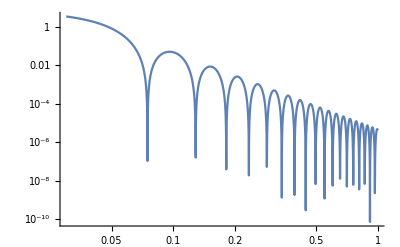

```mathematica
LogLogPlot[hardSphere /. rr->60.0, {xx, 0.03, 1}]
```

## Meeting Notes

Meeting - the guys use SASVIEW
includes marquartd 
some stochastics “dream” method
SASView is heavily dependent on the BUMPS optimiser, whetever we do may have to interface with that.
“easydiffraction” or “easyscience” now with reflectometry looks like a developing ecosystem.  Maybe our library should fit in that.

0.5+ArcTan[50 q]/π

1/50 Tan[(-0.5+p) π]

0.647584

0.937167

0.01

0.1

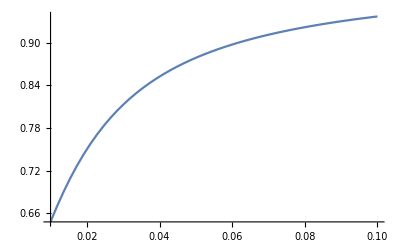

```mathematica
qmin=0.01;
qmax=0.1;
κ=1/50;
cdffunc=(1/π )* ArcTan[q/κ]+0.5
quantilefunc=κ * Tan[π*(p-0.5)]
pmin = cdffunc/.q->qmin
pmax = cdffunc/.q->qmax
genmin=quantilefunc /.p->pmin
genmax=quantilefunc/.p->pmax
Plot[cdffunc,{q,qmin,qmax}]
```

## MCMC Analyses

```mathematica
logExpand[xpr_]:=Module[
{ans,lr1,lr2,lr3,lr4},
lr1=Log[x_^y_]:>y*Log[x];
lr2=Log[x_/y_]:>Log[x]-Log[y];
lr3=Log[x_*y_]:>Log[x]+Log[y];
lr4=Log[Product[x_,{j_,k_}]]:>Sum[Log[x],{j,k}];
Return[xpr//.{lr1,lr2,lr3,lr4}]
]
```

### Porod

On wikipedia, the alpha parameter is 1- the slope parameter, we use alpha = slope parameter.

```mathematica
porodWiki = (α*qmin^α)/q^(α+1)/.α->3
porodcdfWiki = 1-(qmin/x)^α/.α->3
porodQuantileWiki=qmin*(1-p)^(-1/α)/.α->3
```

(3 qmin^3)/q^4

1-qmin^3/x^3

qmin/(1-p)^(1/3)

```mathematica
porodpmf = (α-1)/Qmin*(Q/Qmin)^-α/.α->4
porodcdf=1-(Q/Qmin)^(-α+1)/.α->4
porodquantile=Qmin*(1-p)^(-1/(α-1))/.α->4
```

(3 Qmin^3)/Q^4

1-Qmin^3/Q^3

Qmin/(1-p)^(1/3)

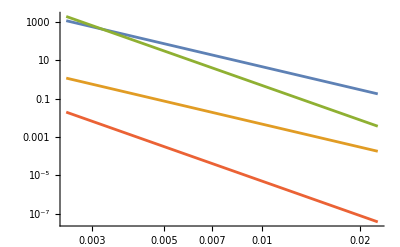

```mathematica
LogLogPlot[
{(α-1)/Qmin*(Q/Qmin)^-α/.{Qmin->0.0025, α->4},

(α-1)/Qmin*(Q/Qmin)^-α/.{Qmin->0.00025, α->4},
(α-1)/Qmin*(Q/Qmin)^-α/.{Qmin->0.0025, α->6},(α-1)/Qmin*(Q/Qmin)^-α/.{Qmin->0.00025, α->6}
},{ Q, 0.0025, 0.0226}]
```

```mathematica
porod=(α-1)/Qmin*(Q/Qmin)^-α
```

((Q/Qmin)^-α (-1+α))/Qmin

```mathematica
q4Int=Integrate[porod/.{Qmin->0.005, α->4},{Q,0.005,0.02}]
q6Int=Integrate[porod/.{Qmin->0.005, α->6},{Q,0.005,0.02}]
```

0.984375

0.999023

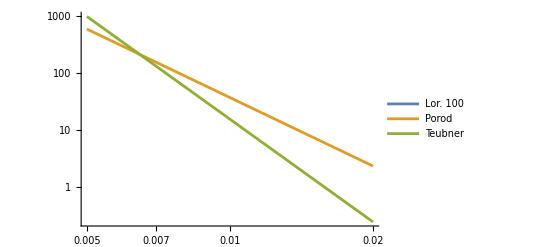

```mathematica
lorGraph=LogLogPlot[
{lor/ lorInt50/.γ->1.0/100.0 ,
porod/.{Qmin->0.005, α->4},
porod/.{Qmin->0.005, α->6}
},{Q,0.005,0.02},
PlotLegends->{
"Lor. 100",
"Porod",
"Teubner"
}]
```

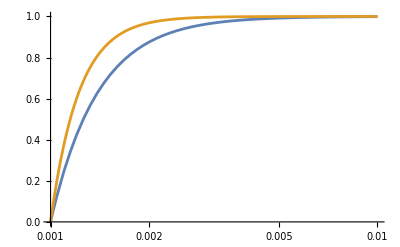

```mathematica
LogLinearPlot[
{1-(Q/Qmin)^(-α+1)/.{Qmin->0.001, α->4},
1-(Q/Qmin)^(-α+1)/.{Qmin->0.001, α->6}
},{ Q, 0.001, 0.01}, PlotRange->{All,{0,1}}]
```

```mathematica
porodpmf = (α-1)/Qmin*(Q/Qmin)^-α
```

((Q/Qmin)^-α (-1+α))/Qmin

```mathematica
porodTerm = porodpmf *Q^4/.α->4
teubnerTerm = porodpmf *Q^6/.α->6
zeta = teubnerTerm / porodTerm
```

3 Qmin^3

5 Qmin^5

(5 Qmin^2)/3

```mathematica
porodcdf=Assuming[{α∈Reals, Qmin∈Reals,0<Qmin<x, α>1}, Integrate[porodpmf, {Q, Qmin, x} ]]
```

1-(Qmin/x)^(-1+α)

```mathematica
porodquantile = Solve[p==porodcdf,x ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(1-p)^(-1/(-1+α)) Qmin}}

1-(Qmin/x)^(-1+α)

### Teubner

```mathematica
teubnerpmf = (α-1)/Qmin*(Q/Qmin)^-α/.α->6
teubnercdf=1-(Qmin/Q)^(α+1)/.α->6
teubnerquantile=Qmin*(1-p)^(-1/(α+1))/.α->6
```

(5 Qmin^5)/Q^6

1-Qmin^7/Q^7

Qmin/(1-p)^(1/7)

```mathematica
qtest=0.2
min=0.001;
testp = porodcdf/.{Qmin->min, Q->qtest}
testq=porodquantile/.{Qmin->min, p->testp}

testp=teubnercdf/.{Qmin->min, Q->qtest}
testq=teubnerquantile/.{Qmin->min, p->testp}
```

0.2

1.

0.200001

1.

0.190207

0.00506226

Lets just derive the whole thing and use emcee for the MCMC  part of the work.  We just need the log likelihood:

```mathematica
like=θ1/(θ2^2+Q^2)+ θ3/Q^4+θ4/Q^6
```

θ1/(Q^2+θ2^2)+θ3/Q^4+θ4/Q^6

```mathematica
loglike=Log[like]
```

Log[θ1/(Q^2+θ2^2)+θ3/Q^4+θ4/Q^6]

```mathematica
logExpand[loglike]
```

Log[θ1/(Q^2+θ2^2)+θ3/Q^4+θ4/Q^6]

```mathematica
simplePorod = 1/x^4
```

1/x^4

```mathematica
porodIntegral=Assuming[{xmin ∈ Reals, xmin>0, xmax ∈Reals,xmax>0}, Integrate[simplePorod, {x, xmin, xmax}]]
```

ConditionalExpression[1/3 (-1/xmax^3+1/xmin^3), xmax≠xmin]

```mathematica
simpleTeubner=1/x^6
```

1/x^6

```mathematica
teubnerIntegral=Assuming[{xmin ∈ Reals, xmin>0, xmax ∈Reals,xmax>0}, Integrate[simpleTeubner, {x, xmin, xmax}]]
```

ConditionalExpression[1/5 (-1/xmax^5+1/xmin^5), xmax≠xmin]

```mathematica
eq1=a+b==1
eq2=a==35*b
```

a+b==1

a==35 b

```mathematica
Solve[{eq1, eq2}, {a,b}]
```

{{a→35/36,b→1/36}}

```mathematica
eqn={
(*q*s==0.006291219764141054,*)
(1-q)*(1-z)==9.196024610951662,
(1-q)*z==330.04356792364206
}
```

{(1-q) (1-z)==9.19602,(1-q) z==330.044}

```mathematica
Solve[eqn, {q,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{q→-338.24,z→0.972892}}

## UnNormalised Porod

```mathematica
porodpdf=Q^-α
porodcdf=Assuming[{α∈Reals, Qmin∈Reals,0<Qmin<Q<Qmax, α>1},Integrate[porodpdf,{Q,Qmin,Qmax}]]/.Qmax->Q
```

Q^-α

((Q Qmin)^-α (Q^α Qmin-Q Qmin^α))/(-1+α)

```mathematica
Solve[p==porodcdf,Q]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Q→(Qmin^-α (p+Qmin/(1-α)) (1-α))^(1/(1-α))}}

## Beta Function Exploration for Mixture Weights

The dirichlet is a multinomal generalisation of a beta distribution, so we’ll start with this for now

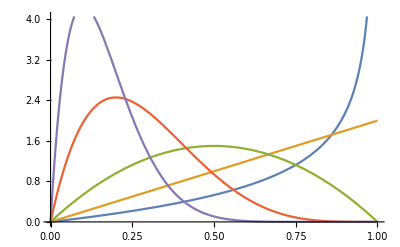

```mathematica
alpha=2;
Plot[Table[PDF[BetaDistribution[alpha,beta],x],{beta, {0.5, 1, 2, 5, 10}}]//Evaluate,{x,0,1}]
```

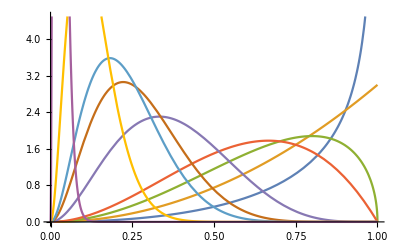

```mathematica
alpha=3;
Plot[Table[PDF[BetaDistribution[alpha,beta],x],{beta, {0.5, 1,1.5, 2, 5,8, 10, 20, 100}}]//Evaluate,{x,0,1}]
```

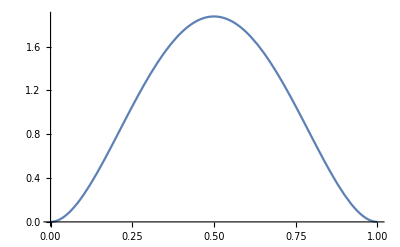

```mathematica
Plot[PDF[BetaDistribution[3,3], x],{x,0,1}]
```

## Conversion of Zeta from Paper LSE to Mixture Weight

```mathematica
lseA=0.26;
lseK=0.25;
lseB=4.5*10^-7;
lseC=1.7*10^-10;
lseZeta=lseC/lseB;
mca= 0.10877056491753044;
mckappa= 0.006907550836517399;
mcb= 0.0009924521192271416;
mcc =0.8902369829632424;
mcZeta = mcc / mcb;

ascale = 1/lseA
cscale = 1 / lseC
bscale = 1 / lseB
(* Assume A is identical in both fits *)
shift=cscale / bscale
mcZeta / shift
lseZeta
```

3.84615

5.88235×10^9

2.22222×10^6

2647.06

2647.06

0.338869

0.000377778

```mathematica
p4=(α-1)/Qmin*(Q/Qmin)^-α/.α->4;
p6=(α-1)/Qmin*(Q/Qmin)^-α/.α->6;
solB=newB/.Solve[oldB == newB*Q^-4/p4, newB][[1]]
solC=newC/.Solve[oldC==newC*Q^-6/p6, newC][[1]]

newZeta = solC/solB
```

3 oldB Qmin^3

5 oldC Qmin^5

(5 oldC Qmin^2)/(3 oldB)

```mathematica
exp=newZeta//.{oldC/oldB -> oZ}
```

(5 oZ Qmin^2)/3

```mathematica
exp /.{oZ->lseZeta, Qmin->0.0025}
```

3.93519×10^-9

```mathematica
lseZeta*3/(5 * 0.0025*0.0025)
```

36.2667